```mathematica
SetOptions[FourierTransform,FourierParameters->{1,-1}];
```

```mathematica
(* Q6 *)
```

```mathematica
(* H(t) is the unit step function. therefore this is an accumulator *)
```

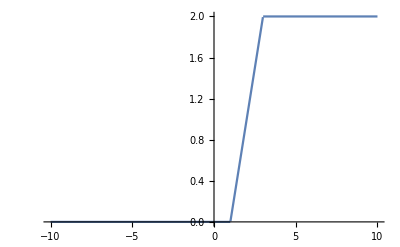

```mathematica
xt[τ_]=Piecewise[{{0,τ<1 || τ>3},{1,3>τ>1}}] ;(* INPUT *)
ht[τ_]:=UnitStep[τ] (* Impulse Response H(t) *) 
yt[τ_]:=Convolve[ht[x],xt[x],x,τ] 
Plot[yt[τ],{τ,-10,10},PlotRange->All]
```

```mathematica
Manipulate[Show[Plot[{ht[(t-τ)],xt[τ]},{τ,-10,10},PlotRange->All,PlotStyle->{Orange,Black,Dashed},Filling->Bottom,
PlotLabel->Style[StringForm["Convolved value at t = ``,   y [ t ] = ``",t,N[yt[t],2]],Red,Bold,Larger]],Plot[yt[c],{c,-10,t}]],{{t,1.1},-5,7}]
```

```mathematica
Convolve[ht[τ],xt[τ],τ,y]
```

Piecewise[{{2, y≥3}, {-1+y, 1<y<3}, {0, True}}]

```mathematica
(* Plot[xt[τ]-yt[τ],{τ,-5,5},PlotRange->All] *)
```